{{1,0.7030.005},{2,0.5710.005},{3,0.4120.006},{4,0.2640.007},{5,0.2140.008},{6,0.2200.007},{7,0.2550.006},{8,0.2460.007},{9,0.2740.007},{10,0.2610.007}}

{{1,0.6470.004},{2,0.5870.004},{3,0.6090.004},{4,0.6040.004},{5,0.6060.004},{6,0.6480.004},{7,0.6830.004},{8,0.7110.004},{9,0.7660.005},{10,0.7980.004}}

{{1,0.75100.0033},{2,0.72060.0030},{3,0.67950.0035},{4,0.67380.0031},{5,0.61840.0031},{6,0.56090.0031},{7,0.57160.0032},{8,0.55460.0032},{9,0.52270.0032},{10,0.53780.0032}}

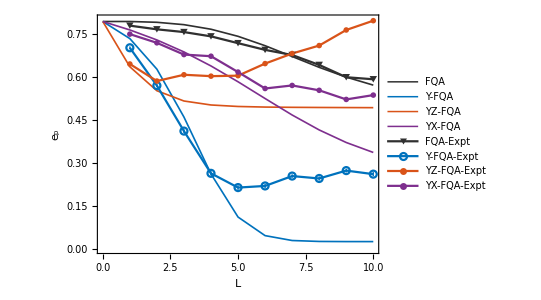

```mathematica
dataF={-1.6000000000000003,-1.6,-1.6112186988051767,-1.6443679258190123,-1.7083184185777482,-1.8074843875028677,-1.9385975788191365,-2.089294725356276,-2.2413472146032403,-2.3779707558615923,-2.49004185355962};
dataFCDyz={-1.6000000000000003,-2.2334470495899725,-2.5684083828392423,-2.7120386006966477,-2.767704374147625,-2.7886639605780035,-2.796901117668267,-2.800578573771387,-2.802597839473322,-2.8040150338739207,-2.8052546529514255};
dataFCDyx={-1.6000000000000003,-1.7181717682385587,-1.8581932932739278,-2.02558432100301,-2.2220256338980735,-2.4431561925077867,-2.677433835549765,-2.9078152120628245,-3.116836552173917,-3.2926242115193656,-3.431801610429116};
dataFCDy={-1.6000000000000003,-1.8392700229319439,-2.2666712462333316,-2.936265422867532,-3.732462126362557,-4.335154531302772,-4.59504045908713,-4.663320886131266,-4.676413580330181,-4.678384780480009,-4.6785644797493005};
dataExpFP={-1.65813688,-1.70954942,-1.74790162,-1.80807361,-1.90327266,-1.99694031,-2.06863802,-2.20754986,-2.37958891,-2.40821412};
dataExpFPstd={0.01608872,0.01624803,0.01722424,0.0150883,0.01443058,0.0142882,0.01418565,0.0145655,0.01632037,0.01787288};
dataExpFCDyP={-1.96755175,-2.49655151,-3.13282555,-3.72381233,-3.9230051,-3.90015401,-3.76191677,-3.79570882,-3.68542535,-3.73513478};
dataExpFCDyPstd={0.01882895,0.01912995,0.02474806,0.02911224,0.03192573,0.02979792,0.02475307,0.02878631,0.02684144,0.02869299};
dataExpFCDyzP={-2.19451691,-2.43306042,-2.34502538,-2.36456698,-2.35783729,-2.18884156,-2.04793886,-1.93654512,-1.71872006,-1.58866838};
dataExpFCDyzPstd={0.01602453,0.01665156,0.01521476,0.01593135,0.01702451,0.01514654,0.01602922,0.01496045,0.01813687,0.01531789};
dataExpFCDyxP={-1.77667554,-1.89856763,-2.06269785,-2.08559436,-2.3072449,-2.53715584,-2.49445766,-2.56255552,-2.69007195,-2.62947978};
dataExpFCDyxPstd={0.01315731,0.01196343,0.01416707,0.01251447,0.01253824,0.01240699,0.0128687,0.01286127,0.01268407,0.01273414};
dataExpFPp=Table[{i,(Around[dataExpFP[[i]],dataExpFPstd[[i]]]+4.780861320010876)/4},{i,Length[dataExpFP]}];
dataExpFCDyPp=Table[{i,(Around[dataExpFCDyP[[i]],dataExpFCDyPstd[[i]]]+4.780861320010876)/4},{i,Length[dataExpFP]}]
dataExpFCDyzPp=Table[{i,(Around[dataExpFCDyzP[[i]],dataExpFCDyzPstd[[i]]]+4.780861320010876)/4},{i,Length[dataExpFP]}]
dataExpFCDyxPp=Table[{i,(Around[dataExpFCDyxP[[i]],dataExpFCDyxPstd[[i]]]+4.780861320010876)/4},{i,Length[dataExpFP]}]
dataFp=Table[{i-1,(dataF[[i]]+4.780861320010876)/4},{i,Length[dataF]}];
dataFCDyP=Table[{i-1,(dataFCDy[[i]]+4.780861320010876)/4},{i,Length[dataFCDy]}];
dataFCDyzP=Table[{i-1,(dataFCDyz[[i]]+4.780861320010876)/4},{i,Length[dataFCDyz]}];
dataFCDyxP=Table[{i-1,(dataFCDyx[[i]]+4.780861320010876)/4},{i,Length[dataFCDyx]}];
Show[ListPlot[{dataFp,dataFCDyP,dataFCDyzP,dataFCDyxP,dataExpFPp,dataExpFCDyPp,dataExpFCDyzPp,dataExpFCDyxPp},PlotRange->All,Joined->{True,True,True,True,True,True,True,True},PlotMarkers->{None,None,None,None,Automatic,Automatic,Automatic,Automatic},PlotLegends->{"FQA","Y-FQA","YZ-FQA","YX-FQA","FQA-Expt","Y-FQA-Expt","YZ-FQA-Expt","YX-FQA-Expt"},PlotStyle->{{RGBColor["#303030"],Thickness[0.003]},{RGBColor["#0072BD"],Thickness[0.003]},{RGBColor["#D95319"],Thickness[0.003]},{RGBColor["#7E2F8E"],Thickness[0.003]},{RGBColor["#303030"]},{RGBColor["#0072BD"]},{RGBColor["#D95319"]},{RGBColor["#7E2F8E"]}},Frame->True,FrameStyle->Thick,FrameTicksStyle->Black,FrameLabel->{{HoldForm["e_p"],None},{HoldForm["L"],None}},PlotLabel->None,LabelStyle->{15,GrayLevel[0]}],Plot[-4.780861320010876,{x,-3,300},PlotStyle->{Gray,Dashed}],AspectRatio->3/4]
```

{{1,0.7030.005},{2,0.5710.005},{3,0.4120.006},{4,0.2640.007},{5,0.2140.008},{6,0.2200.007},{7,0.2550.006},{8,0.2460.007},{9,0.2740.007},{10,0.2610.007}}

{{1,0.71540.0030},{2,0.59100.0032},{3,0.5280.004},{4,0.59280.0029},{5,0.62060.0030},{6,0.7060.021},{7,0.86310.0031},{8,0.95460.0033}}

{{1,0.7030.024},{2,0.5420.023},{3,0.3370.022},{4,-0.0270.016},{5,-0.160.08},{6,-0.290.15},{7,0.030.06},{8,-0.220.16}}

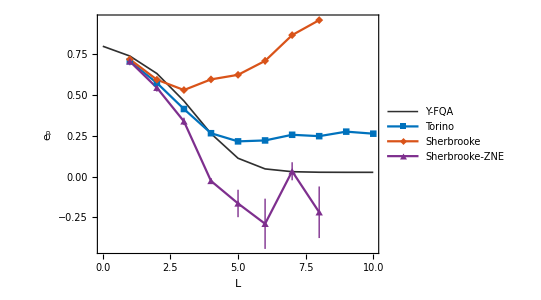

```mathematica
dataFCDy={-1.6000000000000003,-1.8392700229319439,-2.2666712462333316,-2.936265422867532,-3.732462126362557,-4.335154531302772,-4.59504045908713,-4.663320886131266,-4.676413580330181,-4.678384780480009,-4.6785644797493005};
dataExpFCDyPTorino={-1.96755175,-2.49655151,-3.13282555,-3.72381233,-3.9230051,-3.90015401,-3.76191677,-3.79570882,-3.68542535,-3.73513478};
dataExpFCDyPstdTorino={0.01882895,0.01912995,0.02474806,0.02911224,0.03192573,0.02979792,0.02475307,0.02878631,0.02684144,0.02869299};
dataExpFCDyPSherbrooke={-1.9194583,-2.41693973,-2.66955838,-2.40981446,-2.2983332,-1.9574924,-1.32853768,-0.96258038};
dataExpFCDyPstdSherbrooke={0.01219517,0.01275653,0.0145829,0.01172469,0.01215494,0.08283359,0.0123371,0.01304261};
dataExpFCDyPSherbrookeZNE={-1.96963636,-2.6139908,-3.43482235,-4.88903163,-5.43879017,-5.93517566,-4.65293832,-5.65376378};
dataExpFCDyPstdSherbrookeZNE={0.09540386,0.09331274,0.08976502,0.06577211,0.33502178,0.61334953,0.2202557,0.62962442};
dataExpFCDyPTorinoP=Table[{i,(Around[dataExpFCDyPTorino[[i]],dataExpFCDyPstdTorino[[i]]]+4.780861320010876)/4},{i,Length[dataExpFCDyPTorino]}]
dataExpFCDyPSherbrookeP=Table[{i,(Around[dataExpFCDyPSherbrooke[[i]],dataExpFCDyPstdSherbrooke[[i]]]+4.780861320010876)/4},{i,Length[dataExpFCDyPstdSherbrooke]}]
dataExpFCDyPSherbrookeZNEP=Table[{i,(Around[dataExpFCDyPSherbrookeZNE[[i]],dataExpFCDyPstdSherbrookeZNE[[i]]]+4.780861320010876)/4},{i,Length[dataExpFCDyPstdSherbrookeZNE]}]
dataFCDyP=Table[{i-1,(dataFCDy[[i]]+4.780861320010876)/4},{i,Length[dataFCDy]}];
Show[ListPlot[{dataFCDyP,dataExpFCDyPTorinoP,dataExpFCDyPSherbrookeP,dataExpFCDyPSherbrookeZNEP},PlotRange->All,Joined->{True,True,True,True,True,True,True,True},PlotMarkers->{None,Automatic,Automatic,Automatic,Automatic},PlotLegends->{"Y-FQA","Torino","Sherbrooke","Sherbrooke-ZNE"},PlotStyle->{{RGBColor["#303030"],Thickness[0.003]},{RGBColor["#0072BD"]},{RGBColor["#D95319"]},{RGBColor["#7E2F8E"]}},Frame->True,FrameStyle->Thick,FrameTicksStyle->Black,FrameLabel->{{HoldForm["e_p"],None},{HoldForm["L"],None}},PlotLabel->None,LabelStyle->{15,GrayLevel[0]}],Plot[-4.780861320010876,{x,-3,300},PlotStyle->{Gray,Dashed}],AspectRatio->3/4]
```